```mathematica
Limit[(Log[1+2^(-2*a*d)]-Log[2^((a-1)*d-1)+2^(-2*a*d)])/(2(d-1)),d->∞]
```

Limit[(Log[1+2^(-2 a d)]-Log[2^(-2 a d)+2^(-1+(-1+a) d)])/(2 (-1+d)),d→∞]

```mathematica
Plot[(Log[1+2^(-2*a*d)]-Log[2^((a-1)*d-1)+2^(-2*a*d)])/(2(d-1))/.d->,{a,1,100000000}]
```

$Aborted

```mathematica
N[E^.23]
```

1.2586

```mathematica
((1+2^(-2a*d))/(2^((a-1)*d-1) +2^(-2*a*d)))^(1/2/d)
D[((1+2^(-2a*d))/(2^((a-1)*d-1) +2^(-2*a*d)))^(1/2/d), a]
```

((1+2^(-2 a d))/(2^(-2 a d)+2^(-1+(-1+a) d)))^(1/(2 d))

```mathematica
D[((1+2^(-2 a d))/(2^(-2 a d)+2^(-1+(-1+a) d)))^(1/(2 d)), a]
```

(((1+2^(-2 a d))/(2^(-2 a d)+2^(-1+(-1+a) d)))^(-1+1/(2 d)) (-(2^(1-2 a d) d Log[2])/(2^(-2 a d)+2^(-1+(-1+a) d))-((1+2^(-2 a d)) (2^(-1+(-1+a) d) d Log[2]-2^(1-2 a d) d Log[2]))/((2^(-2 a d)+2^(-1+(-1+a) d))^2)))/(2 d)

```mathematica
Solve[(((1+2^(-2 a d))/(2^(-2 a d)+2^(-1+(-1+a) d)))^(-1+1/(2 d)) (-(2^(1-2 a d) d Log[2])/(2^(-2 a d)+2^(-1+(-1+a) d))-((1+2^(-2 a d)) (2^(-1+(-1+a) d) d Log[2]-2^(1-2 a d) d Log[2]))/((2^(-2 a d)+2^(-1+(-1+a) d))^2)))/(2 d)==0,a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→Log[-2^(1/3)/((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))+((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))/2^(1/3)]/(d Log[2])},{a→Log[(1+ⅈ √3)/(2^(2/3) (2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))-((1-ⅈ √3) (2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))/(2 2^(1/3))]/(d Log[2])},{a→Log[(1-ⅈ √3)/(2^(2/3) (2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))-((1+ⅈ √3) (2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))/(2 2^(1/3))]/(d Log[2])}}

```mathematica
Limit[Log[-2^(1/3)/((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))+((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))/2^(1/3)]/(d Log[2]),d->100]
```

Log[(-1+(2535301200456458802993406410752+√6427752177035961102167848369364650410088811975131171341205505)^(2/3))/(2535301200456458802993406410752+√6427752177035961102167848369364650410088811975131171341205505)^(1/3)]/(100 Log[2])

```mathematica
N[%11]
```

0.34

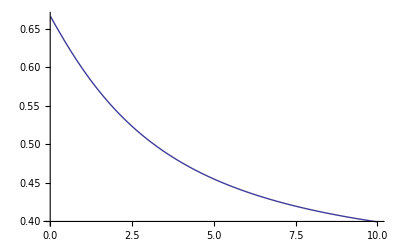

```mathematica
Plot[Log[-2^(1/3)/((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))+((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))/2^(1/3)]/(d Log[2]),{d,0.01,10}]
```

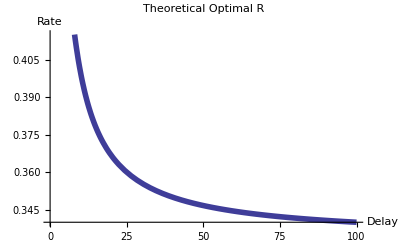

```mathematica
Plot[Log[-2^(1/3)/((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))+((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))/2^(1/3)]/(d Log[2]),{d,0.01,100},PlotStyle->Thickness[0.01],PlotLabel->Style["Theoretical Optimal R",FontSize->24],AxesLabel->{"Delay","Rate"}]
```

```mathematica
Export["150505_fig1",%9,"PDF"]
```

150505_fig1

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["150505_fig1"]]]
```

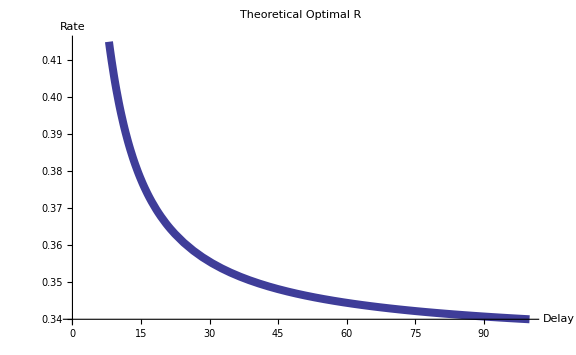

```mathematica
Show[%9,ImageSize->Large]
```

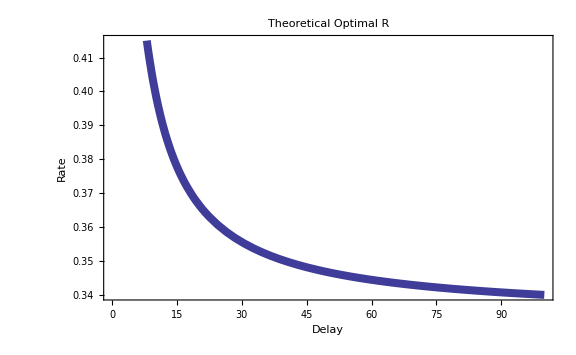

```mathematica
Show[%10,Frame->True,FrameStyle->Black]
```

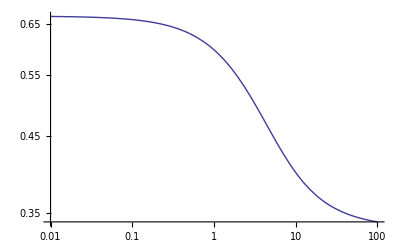

```mathematica
LogLogPlot[Log[-2^(1/3)/((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))+((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))/2^(1/3)]/(d Log[2]),{d,0.01,100}]
```

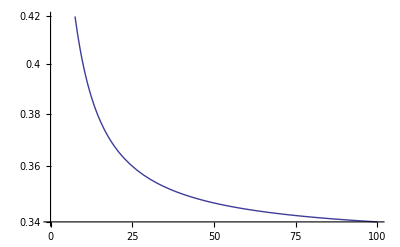

```mathematica
LogPlot[Log[-2^(1/3)/((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))+((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))/2^(1/3)]/(d Log[2]),{d,0.01,100}]
```

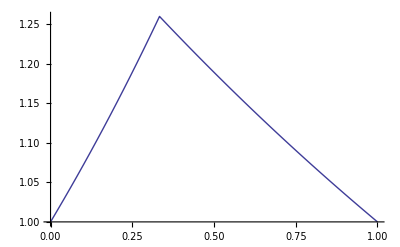

```mathematica
Plot[E^((Log[1+2^(-2*a*d)]-Log[2^((a-1)*d-1)+2^(-2*a*d)])/(2(d)))/.d->10000000,{a,0,1}]
```

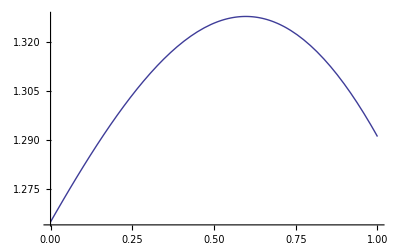

```mathematica
Plot[E^((Log[1+2^(-2*a*d)]-Log[2^((a-1)*d-1)+2^(-2*a*d)])/(2(d)))/.d->1,{a,0,1}]
```

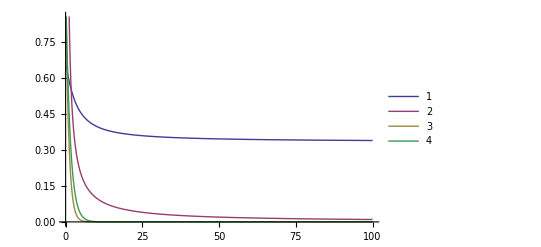

```mathematica
Plot[{Log[-2^(1/3)/((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))+((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))/2^(1/3)]/(d Log[2]),1/d,E^(-d), 2^(-d)},{d,0.01,100},PlotLegends->Automatic]
```

```mathematica
ParametricPlot[{Log[-2^(1/3)/((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))+((2^(2+d)+2 √(1+2^(2+2 d)))^(1/3))/2^(1/3)]/(d Log[2]),},{d,0.01,100}]
```